### Experiment 5: Forced damped harmonic oscillator (Pohl’s Pendulum) Siddharth Ahire(EP20B006) | Shantanu Joshi(EP20B020)

```mathematica
------------------------------------------------------------
```

```mathematica
(*Numerical Solution*)
Solution= NDSolve[{y''[x] + 5*y[x] + 0.5*y'[x] == 0, y[0] == 0.25, y'[0] == 0}, y, 
{x, 0 , 10}]
```

{{y→InterpolatingFunction[…]}}

```mathematica
(*Theorotical case*)
```

```mathematica
theoreticalSol = Partition[Riffle[Table[i,{i,0,10,0.1}],
Flatten[Table[Evaluate[y[i]/.Solution], {i, 0, 10, 0.2}]]],2];
Fitting = FindFit[theoreticalSol,a Exp[b *x]*Cos[d* x  + c] , {a,b,c,d}, x];
theoreticalFit = a Exp[b *x]*Cos[d* x  + c] /. Fitting
```

0.163718 ⅇ^(-0.155238 x) Cos[0.506358-4.84682 x]

```mathematica
(* Adding White Noise to data*)
NoisedData =Partition[Riffle[Table[i,{i,0,10,0.1}],
Flatten[Table[Evaluate[y[i]/.Solution]*RandomReal[{1,0.1}], {i, 0, 10, 0.1}]]],2];
```

```mathematica
(*Least square fitting random noise values*)
LSFit= FindFit[NoisedData,a Exp[b *x](Cos[d* x  + c] ), 
{a,b,c,d}, x];
FittedExp= a Exp[b *x](Cos[d* x  + c] )/. LSFit
```

-0.125731 ⅇ^(-0.223972 x) Cos[9.56376-2.22436 x]

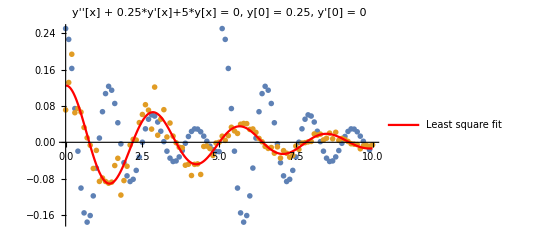

```mathematica
(*Plotting theoretical data, noised data, and the least square fit of noised data*)
S1 = ListPlot[{theoreticalSol, NoisedData},PlotMarkers->{Yellow,Cyan},
PlotLegends -> {"Theoretical Data", "NoisedData"}];
S2 = Plot[FittedExp, {x, 0, 10}, PlotStyle-> Red, 
 PlotLegends -> {"Least square fit"}];
Show[{S1, S2}, PlotLabel -> "y''[x] + 0.25*y'[x]+5*y[x] = 0, y[0] = 0.25, y'[0] = 0", 
PlotRange -> Automatic]
```

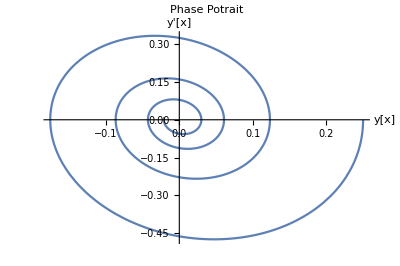

```mathematica
ParametricPlot[Flatten[{y[x] /. Solution, y'[x] /. Solution}], {x, 0, 10}, AxesLabel->{"y[x]", "y'[x]"}, PlotLabel -> "Phase Potrait",AspectRatio->1/1.5]
```

```mathematica
(*Numerical soltion for a underdamped forced oscillator*)
ForcedDamped[t_]=z[t]/.Flatten[ NDSolve[{z''[t]+0.5*z'[t]+20*z[t]-0.3*Cos[0.5*t]==0,z[0]==0.25,z'[0] ==0},z,{t,0,10}]][[1]]
```

InterpolatingFunction[…][t]

```mathematica
ForcedDampedSolution[t_] = DSolve[z''[t]+0.5*z'[t]+20*z[t]-0.3*Cos[0.5*t]==0 &&z[0]==0.25 &&z'[0] ==0,z[t],t]
```

{{z[t]→0.00843867 ⅇ^(-0.25 t) (27.8258 Cos[4.46514 t]+1. ⅇ^(0.25 t) Cos[3.96514 t] Cos[4.46514 t]+0.799743 ⅇ^(0.25 t) Cos[4.46514 t] Cos[4.96514 t]-0.0630494 ⅇ^(0.25 t) Cos[4.46514 t] Sin[3.96514 t]+1.55539 Sin[4.46514 t]+0.0630494 ⅇ^(0.25 t) Cos[3.96514 t] Sin[4.46514 t]+0.0402679 ⅇ^(0.25 t) Cos[4.96514 t] Sin[4.46514 t]+1. ⅇ^(0.25 t) Sin[3.96514 t] Sin[4.46514 t]-0.0402679 ⅇ^(0.25 t) Cos[4.46514 t] Sin[4.96514 t]+0.799743 ⅇ^(0.25 t) Sin[4.46514 t] Sin[4.96514 t])}}

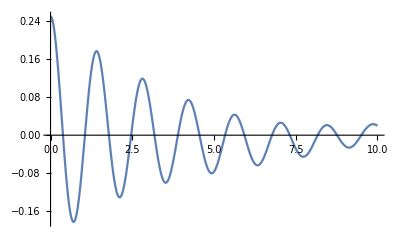

```mathematica
Plot[ForcedDamped[t],{t,0,10}]
```

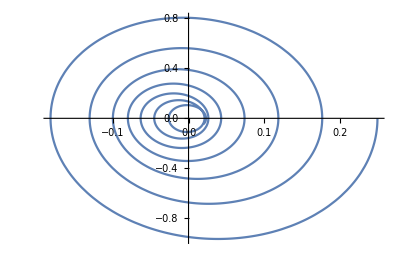

```mathematica
(*Phase Potrait for the numerical solution for the underdamped force Oscillator*)
ParametricPlot[{ForcedDamped[t],ForcedDamped'[t]},{t,0,10},AspectRatio->1/1.5]
```